# Comparing DRG with Exact computations

## Example: L=4 XXZ line

We consider a 1D spin chain with L sites.

## Exact Computations

```mathematica
λ = 4;
hz=-0.02;
hx= 0;
hy= 0;
Ja=1;
```

### Spin-1/2 Operators

We define the spin-1/2 operators where 
S_x = 1/2(0 | 1
1 | 0), S_y = 1/2(0 | -I
I | 0), S_z = 1/2(1 | 0
0 | -1)
and
S_+ = S_x + I S_y = (0 | 1
0 | 0), S_- =S_x -I S_y =(0 | 0
1 | 0).

```mathematica
Sp = {{0,0},{1, 0}};
Sm= {{0,1}, {0,0}};
Sz = {{1/2, 0}, {0 ,-1/2}};
Sx = {{0, 1/2}, {1/2 ,0}};
Sy = {{0, -I}, {I ,0}};
Ops ={Sp, Sm, Sz, IdentityMatrix[2]};
```

### Local Hamiltonian

```mathematica
h = ((Ja/2)(KroneckerProduct[Sp, Sm] + KroneckerProduct[Sm, Sp]) + Ja(KroneckerProduct[Sz, Sz]));
```

### Hamiltonian

```mathematica
H = -Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h,IdentityMatrix[2^(λ-k-1)] ], {k, 1, λ-1}] +Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sz, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hx Sx, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sy, IdentityMatrix[2^(λ-k)]], {k, 1, λ}];
```

### Eigenvalues

```mathematica
Evals =Sort[N[Eigensystem[H][[1]]]]
```

{-0.839443,-0.794721,-0.75,-0.705279,-0.660557,-0.501828,-0.457107,-0.412385,-0.116025,0.205279,0.25,0.294721,0.912385,0.957107,1.00183,1.61603}

### Partition Function

```mathematica
Zexact[β_] := Sum[Exp[-β Evals[[k]]], {k, 1, Length[Evals]}]
```

### Correlation function

```mathematica
Sz1 = KroneckerProduct[IdentityMatrix[2],Sz, IdentityMatrix[2^(λ-2)]];
```

```mathematica
ESz1[β_]:= Tr[Sz1.MatrixExp[- β H]]/ Zexact[β];
```

```mathematica
Sort[Table[{Eigensystem[H][[1]][[k]], ConjugateTranspose[Eigensystem[H][[2]][[k]]].Sz1.Eigensystem[H][[2]][[k]]/Norm[Eigensystem[H][[2]][[k]]]^2}, {k, 1, 16}]]//N
```

{{-0.839443,0.223607+0. ⅈ},{-0.794721,0.111803+0. ⅈ},{-0.75,-8.74301×10^-16+0. ⅈ},{-0.705279,-0.111803+0. ⅈ},{-0.660557,-0.223607+0. ⅈ},{-0.501828,0.19086+0. ⅈ},{-0.457107,1.36002×10^-15+0. ⅈ},{-0.412385,-0.19086+0. ⅈ},{-0.116025,3.33067×10^-16+0. ⅈ},{0.205279,0.111803+0. ⅈ},{0.25,2.498×10^-16+0. ⅈ},{0.294721,-0.111803+0. ⅈ},{0.912385,0.0327465+0. ⅈ},{0.957107,2.03657×10^-15+0. ⅈ},{1.00183,-0.0327465+0. ⅈ},{1.61603,-4.85723×10^-17+0. ⅈ}}

## DMRG

### Eigenvalues

```mathematica
EvalsDMRG = {-0.789999999999998,-0.7843304055971139,-0.7516270709865368,-0.7305694084876648,-0.71388821912133,-0.5671646938259722,-0.464543538652116,-0.447588311089416,-0.11635448626225058,0.011099735780816584,0.23791699845966965};
```

### Partition Function

```mathematica
Zdmrg[β_] := Sum[Exp[-β EvalsDMRG[[k]]], {k, 1, Length[EvalsDMRG]}]
```

### Correlation Function

```mathematica
Sz1DMRG={0.49999999999997385,0.4314327174396475,0.022066255129364082,-0.24461424323958045,-0.44205559502745095,0.14289853674971467,0.15243871970344428,-0.21602017234466392,0.005253548705354975,-0.057512908025683686,0.14905220411765358};
```

```mathematica
ESz1DMRG[β_]:= Sum[Sz1DMRG[[k]]Exp[-β EvalsDMRG[[k]]], {k, 1, Length[EvalsDMRG]}]/Zdmrg[β]
```

## Comparison

### Partition Function

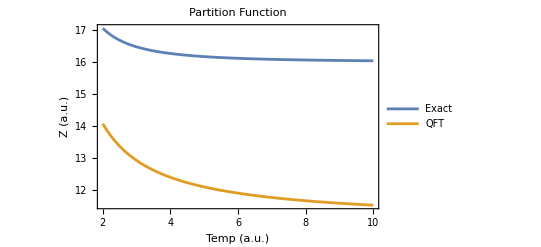

```mathematica
Plot[{Zexact[1/T], Zdmrg[1/T]}, {T, 2, 10},  Frame->True, PlotLegends->{Text[Style["Exact", Bold, Black, 14]], Text[Style["QFT", Bold, Black, 14]]}, PlotLabel->Text[Style["Partition Function", Bold, Black, 14]], FrameLabel->{Text[Style["Temp (a.u.)", Bold, Black, 14]], Text[Style[" Z (a.u.)", Bold, Black, 14]]}]
```

Partition function don’t match because of the dimensional reduction in DMRG.

### Correlation Function

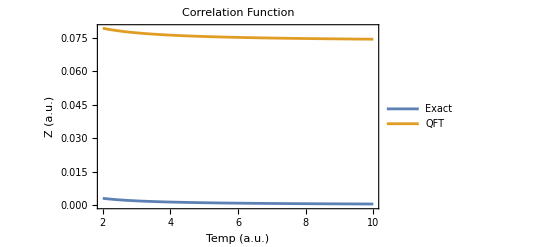

```mathematica
Plot[{ESz1[1/T],ESz1DMRG[1/T]}, {T, 2, 10}, Frame->True, PlotLegends->{Text[Style["Exact", Bold, Black, 14]], Text[Style["QFT", Bold, Black, 14]]}, PlotLabel->Text[Style["Correlation Function", Bold, Black, 14]], FrameLabel->{Text[Style["Temp (a.u.)", Bold, Black, 14]], Text[Style[" Z (a.u.)", Bold, Black, 14]]}]
```